```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookDirectory[]
```

C:\Users\lenovo\source\repos\metvych_lab_3\metvych_lab_3\

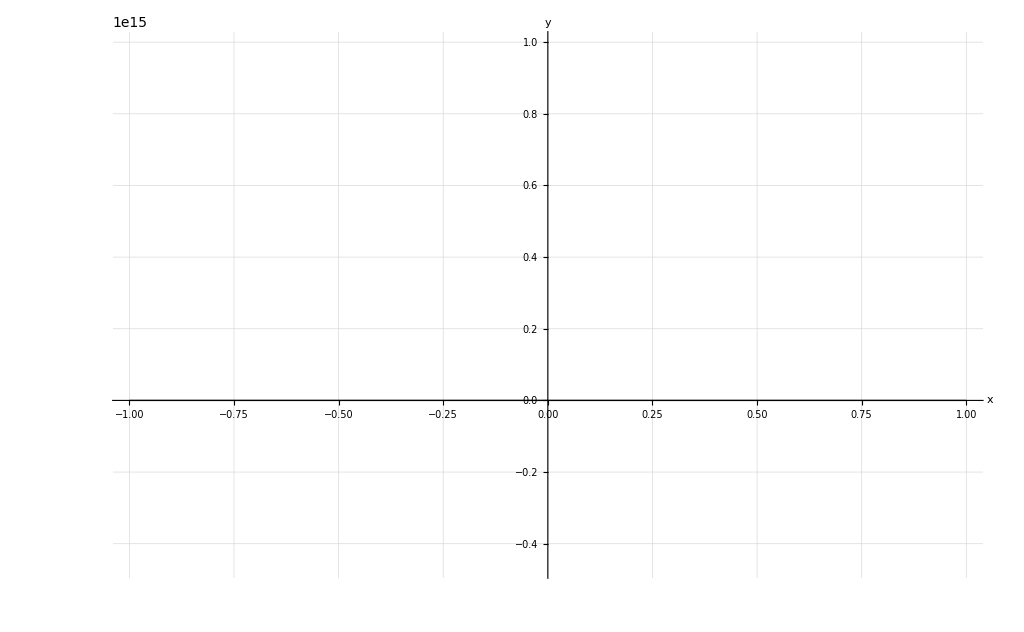

```mathematica
n=2;
ISize:=1024;
color:={{Purple,Thick},{Blue,Thick},{Green,Thick},{Red,Thick}};
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"mass.txt"]],Table[Real,n+1]];
tstart=plots⟦1⟧⟦1⟧;
tend =plots⟦Length[plots]⟧⟦1⟧;
T[i_]:=ArrayFlatten[{plots⟦All,1⟧,plots⟦All,i+1⟧}];
(*ListLinePlot[Table[Transpose[T[i]],{i,1,n}]]*)
plot=ListLinePlot[Table[Transpose[T[i]],{i,1,n}],AxesOrigin->{0,0},PlotRange->{{tstart,tend },All},ImageSize->ISize,
PlotStyle->color,
AxesLabel->{Style["x",Large,Bold,Black, FontFamily->"Times"],Style["y",Large,Bold,Black, FontFamily->"Times"]},
LabelStyle->{Black, FontFamily->"Times"},
AxesStyle->Directive[Arrowheads[{0,0.03}],Thick,Large],
AxesOrigin->{0,0},
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed]
]
```

```mathematica
Export[Evaluate[StringJoin[NotebookDirectory[],"\\plot.png"]],plot]
```

C:\Users\lenovo\source\repos\metvych_lab_3\metvych_lab_3\\plot.png